# Constrain the power-law mass function of Primordial black holes (PBH) using LIGO’s events

## Setup

Model name

```mathematica
model="power-law-PBH-Liu-O1O2";
```

Set the directory

```mathematica
SetDirectory[NotebookDirectory[]];
If[Not[DirectoryQ["backups"]],CreateDirectory["backups"]];
Needs["ErrorBarPlots`"];
Off[Power::infy,Infinity::indet,NDSolve::nlnum,NIntegrate::slwcon];
(*
Needs["NumericalCalculus`"];
Off[General::obspkg,NIntegrate::inumr,NIntegrate::ncvb,NIntegrate::inumri ,NIntegrate::izero];
$TextStyle={FontFamily->"Times",FontSize->7};
*)
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Plot options

```mathematica
plotOptions=Sequence[FrameStyle->(FontFamily->"Times"),BaseStyle->FontSize->18,LabelStyle->Black,Frame->True,Axes->False,PlotRangePadding->None,ImageSize->500,AspectRatio->1];
dx2={1/2,4/2};
contourPlotOptions=Sequence[PlotRange->All,ContourShading->{White,LightRed,Red}];
```

Grid plots for marginalized posteriors

```mathematica
emptyGraph=Graphics[White];
```

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w- 4/5*sidePadding-1)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+4/5*sidePadding;
heights=(h- sidePadding-1)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,4/5*sidePadding,0],1},{If[j==1,sidePadding,0],1}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

## Data

Read LIGO’s data

## Mass data

There are 12 data points in total.

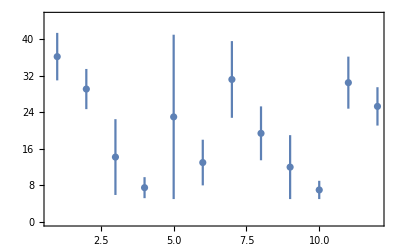

```mathematica
data=ReadList["./LIGO-data/LIGO.txt",{Word,Number,Number,Number,Number,Number,Number}];
nBinary=Length@data;
nobs=2*nBinary;(* N observation *)
Print["There are ",nobs," data points in total."]
Do[name[i]=data[[Ceiling[i/2],1]],{i,1,nobs}];
Do[If[i//OddQ,m[i]=data[[Ceiling[i/2],2]],m[i]=data[[i/2,5]]],{i,1,nobs}];
Do[
If[i//OddQ,
σ[i]=Max[data[[Ceiling[i/2],3]],data[[Ceiling[i/2],4]]],
σ[i]=Max[data[[i/2,6]],data[[i/2,7]]]
],{i,1,nobs}];
plscp=ErrorListPlot[
Table[{m[i],σ[i]},{i,1,nobs}],
Frame->True,
Axes->False,
PlotRange->{All,{0,45}}
]
```

```mathematica
Print["There are ",nBinary," binaries in total."]
binary=Table[Null,nBinary];
For[i=1,i≤nBinary,i++,binary[[i]]={data[[i,2]],Min[data[[i,3]],data[[i,4]]],data[[i,5]],Min[data[[i,6]],data[[i,7]]]}]
binary
```

There are 6 binaries in total.

{{36.2,3.8,29.1,3.7},{14.2,3.7,7.5,2.3},{23,6,13,4},{31.2,6.,19.4,5.3},{12,2,7,2},{30.5,3.,25.3,2.8}}

## Posteriors

### O1 data

```mathematica
eventnames={"GW150914","GW151226","LVT151012"};
Clear[pdm1m2,data,𝒟,i,pdftmp];
pdftmp={};
data[i_?NumberQ]:=ReadList["./LIGO-data/"<>eventnames[[i]]<>"_posterior.txt",{Number,Number}];
𝒟[i_?NumberQ]:=SmoothKernelDistribution[data[i]]

For[i=1,i<=Length@eventnames,i++,
AppendTo[pdftmp,PDF[𝒟[i],{m1,m2}]]
]
(*
For[i=1,i<=3,i++,pdf[i,m1_,m2_]=pdftmp[[i]]]
*)
For[i=1,i<=3,i++,pdm1m2[i,m1_,m2_]=PDF[EstimatedDistribution[data[i],BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ]],{m1,m2}]]
```

```mathematica
Plot3D[pdm1m2[1,m1,m2],{m1,25,53},{m2,20,38},PlotRange->All,PlotPoints->40]
```

-Graphics3D-

### Data beyond O1

```mathematica
If[nBinary≥4,
For[i=4,i≤nBinary,i++,
pdm1m2[i,m1_,m2_]=PDF[BinormalDistribution[{binary[[i,1]],binary[[i,3]]},{binary[[i,2]],binary[[i,4]]},0],{m1,m2}]
]
]

i=4;
Plot3D[pdm1m2[i,m1,m2],{m1,8,53},{m2,5,38},PlotRange->All,PlotPoints->40]
NIntegrate[pdm1m2[i,m1,m2],{m1,5,95},{m2,5,95},PrecisionGoal->3]
Clear@i;
```

-Graphics3D-

0.996589

LIGO’s Volume Sensitivity

## VT- interpolation

```mathematica
VTDataList=ReadList["./Backup/VT_1yr_LIGO_O1.txt",{Number,Number,Number}];
LIGOObservationTimeO1=46.1;(* days or 48.6 days *)
LIGOObservationTimeO2=117;(* days *)
LIGOObservationTimeO1AndO2=LIGOObservationTimeO1+LIGOObservationTimeO2;
timeFraction=LIGOObservationTimeO1AndO2/365;
VT1year=Interpolation@VTDataList;
VTInter[m1_,m2_]:=timeFraction*VT1year[m1,m2]
```

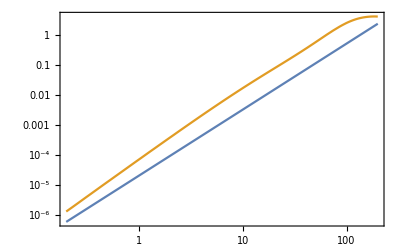

```mathematica
LogLogPlot[{m^2.2/(5*10^4),VTInter[m/2,m/2]},{m,0.20,200},Frame->True]
```

## Merger rate

Original PDF function

130^-α (-130+130^α) (1/M)^(1-α)

1

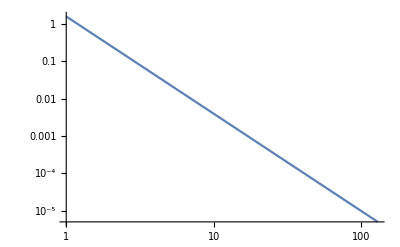

```mathematica
Clear[Ppower,min,max];
Evaluate[min/@{"logf","logM","α","logR"}]={-4,0,1.01,-1};
Evaluate[max/@{"logf","logM","α","logR"}]={-1,Log10@15,4,4};
{min["f"],max["f"]}={10^min["logf"],10^max["logf"]};
{min["M"],max["M"]}={10^min["logM"],10^max["logM"]};
{min["R"],max["R"]}={10^min["logR"],10^max["logR"]};
{logf0,logM0,α0,R0,logR0}={-3,Log10@5,1.6,100,2};
Mmin=1;
mMin=min["M"];
mTotMax=130;
mMax=130;
Ppower[i_,α_,M_:5]:=(α-1)/M*(i/M)^-α;
Integrate[Ppower[ii,α,M],{ii,mMin,mMax},Assumptions->α>1]
Integrate[Ppower[ii,α,M],{ii,M,∞},Assumptions->α>1&&M>0]
LogLogPlot[Ppower[i,α0]/i,{i,mMin,mMax},PlotRange->All]
```

Binary PDF function

```mathematica
Integrate[Ppower[ii,α,M]/ii,{ii,M,∞},Assumptions->α>1&&M>0]
```

(-1+α)/(M α)

```mathematica
mpbhpower[α_,M_:5]:=((-1+α)/(M α))^-1

Ppower[i,α,M]*mpbhpower[α,M]/i
```

((i/M)^-α α)/i

```mathematica
mpbhpower[α_,M_:5]:=((-1+α)/(M α))^-1
Fpower[i_,α_,M_]:=((i/M)^-α α)/i;
Integrate[Fpower[ii,α,M],{ii,M,∞},Assumptions->α>1&&M>0]
```

1

```mathematica
{m10,m20}={30,30};
logM0=0.8714109083376727;
M0=7.437224791850505;
logf0=-2.5487351805854974;
f0=0.002826603025098389;
α0=2.4081116862468503;
```

```mathematica
1.32*10^6*(0.85)^(53/37)
```

1.03001×10^6

```mathematica
Integrate[l^(-21/37)*Fpower[l,α,M],{l,M,∞},Assumptions->α>1&&M>0]
```

(37 α)/(M^(21/37) (21+37 α))

```mathematica
1.32*10^6 fpbh^(53/37)/mpbhpower[α,M]^(53/37)(i*j)^(3/37)(i+j)^(36/37) Fpower[i,α,M]*Fpower[j,α,M]*  (37 α)/(M^(21/37) (21+37 α))//FullSimplify
```

(4.884×10^7 fpbh^(53/37) (i+j)^(36/37) (i/M)^-α (j/M)^-α α^3)/((i j)^(34/37) M^(21/37) ((M α)/(-1+α))^(53/37) (21+37 α))

```mathematica
Clear[i,mergerRateDensity1st]
mergerRateDensity1st[f_,i_,j_,α_,M_:5]:=(4.884*^7 fpbh^(53/37) (i+j)^(36/37) (i/M)^-α (j/M)^-α α^3)/((i j)^(34/37) M^(21/37) ((M α)/(-1+α))^(53/37) (21+37 α))
```

```mathematica
(*Clear[normalFactorMergerRateDensity1st,normalizedMergerRateDensity1st];
normalFactorMergerRateDensity1st[f_?NumericQ,α_?NumericQ,M_:5]:=NIntegrate[mergerRateDensity1st[f,m1,m2,α,M],{m1,M,mMax},{m2,M,mMax},PrecisionGoal->3];

normalizedMergerRateDensity1st[f_,i_,j_,α_,M_:5]:=mergerRateDensity1st[f,i,j,α,M]/normalFactorMergerRateDensity1st[f,α,M];
normalFactorMergerRateDensity1st[f0,α0]
normalizedMergerRateDensity1st[f0,m10,m20,α0]
NIntegrate[normalizedMergerRateDensity1st[f0,m1,m2,α0],{m1,M0,mMax},{m2,M0,mMax},PrecisionGoal->3]*)
```

```mathematica
Integrate[l^(-42/37)*Fpower[l,α,M],{l,M,∞},Assumptions->α>1&&M>0]
```

(37 α)/(M^(42/37) (42+37 α))

```mathematica
1.59*10^4*fpbh^(69/37)/mpbhpower[α,M]^(69/37)k^(6/37)(i+j)^(6/37)(i+j+k)^(72/37)Fpower[i,α,M]*Fpower[j,α,M]*Fpower[k,α,M]*(37 α)/(M^(42/37) (42+37 α))//FullSimplify
```

(588300. fpbh^(69/37) (i+j)^(6/37) (i+j+k)^(72/37) (i/M)^(-1-α) (j/M)^-α (k/M)^-α α^4)/(j k^(31/37) M^(79/37) ((M α)/(-1+α))^(69/37) (42+37 α))

```mathematica
Mergersecond2[fpbh_,i_,j_,k_,α_,M_]:=(588300 fpbh^(69/37) (i+j)^(6/37) (i+j+k)^(72/37) (i/M)^(-1-α) (j/M)^-α (k/M)^-α α^4)/(j k^(31/37) M^(79/37) ((M α)/(-1+α))^(69/37) (42+37 α));
Integrate[Mergersecond2[f,e,i-e,j,α,M],{e,M,i-M},Assumptions->0<2*M≤i&&j>0]
```

(588300 f^(69/37) i^(-2 α) j^-α (i+j)^(72/37) M^(-3+3 α) α^4 (-Beta[M/i,-α,-α]+Beta[1-M/i,-α,-α]))/((i j)^(31/37) (α/(-1+α))^(69/37) (42+37 α))

```mathematica
fpbh=0.0025693801260000975 ;
M=8.896735628637506;
α=1.9108320383237213;
i=10;
j=30;
mergerRateDensity1st[f,i,j,α,M]
```

0.0475548

```mathematica
mergerRateDensity2nd0[10^-3,12,20,1.3,5]
```

0.0000148263

```mathematica
Clear@mergerRateDensity2nd0;
mergerRateDensity2nd0[f_,i_,j_,α_,M_:5]:=If[i>2*M,(588300 f^(69/37) i^(-2 α) j^-α (i+j)^(72/37) M^(-3+3 α) α^4 (-Beta[M/i,-α,-α]+Beta[1-M/i,-α,-α]))/((i j)^(31/37) (α/(-1+α))^(69/37) (42+37 α)),0];

mergerRateDensity2nd[f_,i_,j_,α_,M_:5]:=1/2*(mergerRateDensity2nd0[f,i,j,α,M]+mergerRateDensity2nd0[f,j,i,α,M])

mergerRateDensity2nd0[f0,m10,m20,α0]//AbsoluteTiming
mergerRateDensity2nd[f0,m10,m20,α0]//AbsoluteTiming
```

{0.00001,If[m10>10,(588300 f0^(69/37) m10^(-2 1.6) m20^-1.6 (m10+m20)^(72/37) 5^(-3+3 1.6) 1.6^4 (-Beta[5/m10,-1.6,-1.6]+Beta[1-5/m10,-1.6,-1.6]))/((m10 m20)^(31/37) (1.6/(-1+1.6))^(69/37) (42+37 1.6)),0]}

{0.000017,1/2 (If[m10>10,(588300 f0^(69/37) m10^(-2 1.6) m20^-1.6 (m10+m20)^(72/37) 5^(-3+3 1.6) 1.6^4 (-Beta[5/m10,-1.6,-1.6]+Beta[1-5/m10,-1.6,-1.6]))/((m10 m20)^(31/37) (1.6/(-1+1.6))^(69/37) (42+37 1.6)),0]+If[m20>10,(588300 f0^(69/37) m20^(-2 1.6) m10^-1.6 (m20+m10)^(72/37) 5^(-3+3 1.6) 1.6^4 (-Beta[5/m20,-1.6,-1.6]+Beta[1-5/m20,-1.6,-1.6]))/((m20 m10)^(31/37) (1.6/(-1+1.6))^(69/37) (42+37 1.6)),0])}

```mathematica
NIntegrate[(t*(1-t))^-5,{t,0.1, 0.5}]
```

5369.66

```mathematica
Clear@mergerRateDensity;
mergerRateDensity[f_?NumericQ,i_?NumericQ,j_?NumericQ,α_?NumericQ,M_:5]:=mergerRateDensity1st[f,i,j,α,M]+mergerRateDensity2nd[f,i,j,α,M];

mergerRateDensity[f0,m10,m20,α0]//AbsoluteTiming
NIntegrate[mergerRateDensity[f0,m1,m2,α0,M0],{m1,M0,mMax},{m2,M0,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

{0.000517,0.000353813}

49.2469

```mathematica
ratioR[f_?NumericQ,i_?NumericQ,j_?NumericQ,α_?NumericQ,M_:5]:=mergerRateDensity2nd[f,i,j,α,M]/mergerRateDensity1st[f,i,j,α,M];
```

```mathematica
R1=NIntegrate[mergerRateDensity1st[f0,m1,m2,α0,M0],{m1,M0,mMax},{m2,M0,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
R2=NIntegrate[mergerRateDensity2nd[f0,m1,m2,α0,M0],{m1,M0,mMax},{m2,M0,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

R2/R1
```

48.9994

0.247273

0.00504644

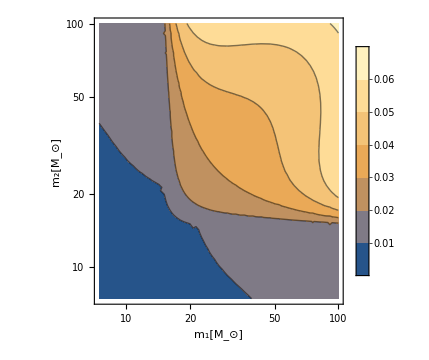

```mathematica
ContourPlot[ratioR[f0,i,j,α0,M0],{i,M0,mMax},{j,M0,mMax},FrameLabel->{"m_1[M_⊙]","m_2[M_⊙]"},ScalingFunctions->{"Log","Log"},FrameStyle->FontFamily->"Times",BaseStyle->FontSize->14,LabelStyle->GrayLevel[0],Frame->True,Axes->False,PlotRangePadding->None,ImageSize->360,AspectRatio->1,PlotLegends->Automatic]
(*Export["../latex/ratio-power.pdf",%]*)
```

```mathematica
Clear@R0;
R0[f_?NumericQ,α_?NumericQ,M_:M0]:=R0[f,α,M]=NIntegrate[mergerRateDensity[f,m1,m2,α,M],{m1,M,mMax},{m2,M,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
R0[f0,α0]//AbsoluteTiming
```

{0.071704,49.2469}

## Likelihood

## β2Inter - Interpolation of β2

```mathematica
βR0Inter=Interpolation@Import[".//backups//"<>model<>"_βR0Data"<>".m"]
Plot3D[βR0Inter[logf0,α,logM],{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PlotRange->All]
```

InterpolatingFunction[…]

-Graphics3D-

pdαSumInter - Interpolation of pdαSum

```mathematica
pdSumInter=Interpolation@Import[".//backups//"<>model<>"_pdSumData"<>".m"]
Plot3D[pdSumInter[logf0,α,logM],{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PlotRange->All]
```

InterpolatingFunction[…]

-Graphics3D-

## Posteriors

```mathematica
postNorm=NIntegrate[10^logf*10^logM*ⅇ^(-βR0Inter[logf,α,logM])*ⅇ^pdSumInter[logf,α,logM],{logf,min["logf"],max["logf"]},{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

3.04081×10^-17

```mathematica
post[logf_?NumericQ,α_?NumericQ,logM_?NumericQ]:=post[logf,α,logM]=1/postNorm*10^logf*10^logM*ⅇ^(-βR0Inter[logf,α,logM])*ⅇ^pdSumInter[logf,α,logM]

post[logf0,α0,logM0]//AbsoluteTiming

NIntegrate[post[logf,α,logM],{logf,min["logf"],max["logf"]},{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

{0.000122,0.0112318}

1.

## Contour plots

1D Marginalized posteriors

## Credible intervals

```mathematica
Clear[cdf,lower,upper,median];
```

```mathematica
cdf[para_?StringQ,y_?NumericQ]:=cdf[para,y]=NIntegrate[marginalPosterior1D[para,x],{x,min[para],y},PrecisionGoal->3];lower[para_?StringQ]:=lower[para]=x/.FindRoot[cdf[para,x]==0.05,{x,min[para],max[para]},PrecisionGoal->3];
upper[para_?StringQ]:=upper[para]=x/.FindRoot[cdf[para,x]==0.95,{x,min[para],max[para]},PrecisionGoal->3];
median[para_?StringQ]:=median[para]=x/.FindRoot[cdf[para,x]==0.5,{x,min[para],max[para]},PrecisionGoal->3];

minus[x_?StringQ]:=lower[x]-median[x];
plus[x_?StringQ]:=upper[x]-median[x];
range[x_?StringQ]:={lower[x],median[x],upper[x],plus[x],minus[x]}
```

## logf parameter

```mathematica
NIntegrate[post[logf,α,logM],{logf,min["logf"],max["logf"]},{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

1.

```mathematica
marginalPosterior1D["logf",logf_?NumericQ]:=marginalPosterior1D["logf",logf]=NIntegrate[post[logf,α,logM],{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

NIntegrate[marginalPosterior1D["logf",logf],{logf,min["logf"],max["logf"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{10.8679,1.00027}

```mathematica
range["logf"]//AbsoluteTiming
10^(%[[2]])
Table[cdf["logf",range["logf"][[ii]]],{ii,3}]
```

{139.465,{-2.78192,-2.54874,-2.33827,0.233184,0.210461}}

{0.00165227,0.0028266,0.00458908,1.71074,1.62353}

{0.05,0.5,0.95}

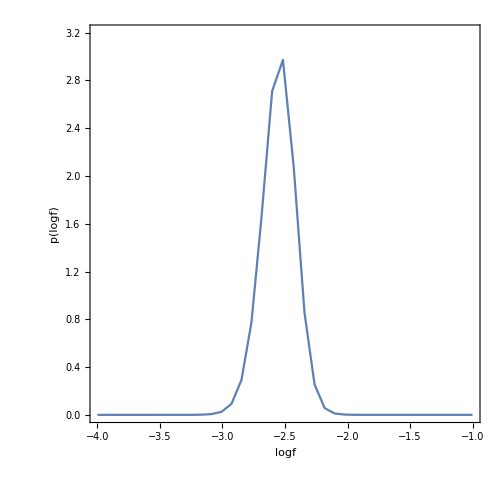

```mathematica
plot1D["logf"]=Plot[marginalPosterior1D["logf",logf],{logf,min["logf"],max["logf"]},PlotRange->{All,{0.0,3.2}},Evaluate@plotOptions,PlotPoints->10,MaxRecursion->2,FrameLabel -> {"logf", "p(logf)"}]
```

## α parameter

```mathematica
marginalPosterior1D["α",α_?NumericQ]:=marginalPosterior1D["α",α]=NIntegrate[post[logf,α,logM],{logf,min["logf"],max["logf"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

NIntegrate[marginalPosterior1D["α",α],{α,min["α"],max["α"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{11.5719,1.00026}

```mathematica
range["α"]//AbsoluteTiming
Table[cdf["α",range["α"][[ii]]],{ii,3}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{236.543,{1.53342,2.40811,3.40679,0.874687,0.998675}}

{0.05,0.500531,0.95}

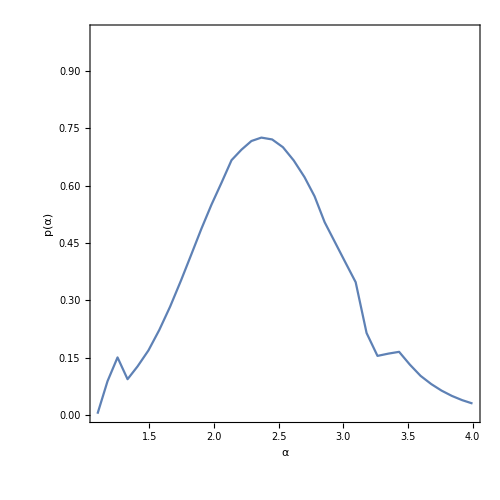

```mathematica
plot1D["α"]=Plot[marginalPosterior1D["α",α],{α,1.1,max["α"]},PlotRange->{All,{0,1.0}},Evaluate@plotOptions,PlotPoints->10,MaxRecursion->2,FrameLabel -> {"α", "p(α)"}]
```

## logM parameter

```mathematica
marginalPosterior1D["logM",logM_?NumericQ]:=marginalPosterior1D["logM",logM]=NIntegrate[post[logf,α,logM],{α,min["α"],max["α"]},{logf,min["logf"],max["logf"]},PrecisionGoal->3]

NIntegrate[marginalPosterior1D["logM",logM],{logM,min["logM"],max["logM"]},PrecisionGoal->3]
```

1.00044

```mathematica
range["logM"]//AbsoluteTiming
10^(%[[2]])
Table[cdf["logM",range["logM"][[ii]]],{ii,3}]
```

{149.579,{0.614249,0.871411,0.945433,0.257162,0.0740221}}

{4.11386,7.43722,8.81928,1.80785,1.18583}

{0.05,0.5,0.95}

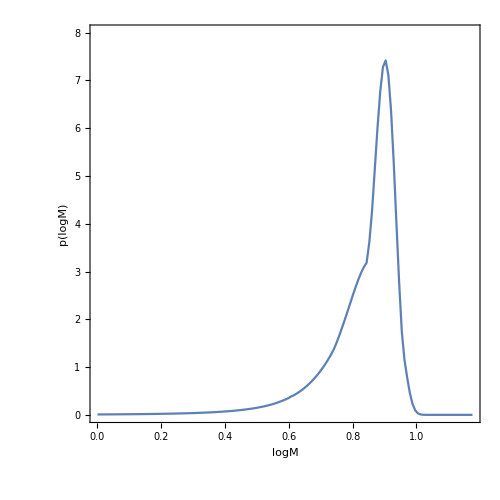

```mathematica
plot1D["logM"]=Plot[marginalPosterior1D["logM",logM],{logM,min["logM"],max["logM"]},PlotRange->{All,{0.0,8}},Evaluate@plotOptions,PlotPoints->10,MaxRecursion->4,FrameLabel -> {"logM", "p(logM)"}]
```

## R parameter

```mathematica
{10^median["logf"],median["α"],10^median["logM"]}
```

{0.0028266,2.40811,7.43722}

```mathematica
R0Fit=R0[10^median["logf"],median["α"],10^median["logM"]]
```

49.2469

```mathematica
βR0Inter[median["logf"],median["α"],median["logM"]]
```

6.81701

```mathematica
R0Post[R0_]:=R0^nBinary*ⅇ^(-R0 βR0Inter[median["logf"],median["α"],median["logM"]]/R0Fit)
```

```mathematica
normR=NIntegrate[R0Post[R],{R,min["R"],max["R"]}];
marginalPosterior1D["R",R_?NumericQ]:=R0Post[R]/normR;

NIntegrate[marginalPosterior1D["R",R],{R,min["R"],max["R"]}]
```

1.

```mathematica
range["R"]//AbsoluteTiming
```

{0.128057,{23.7335,48.1822,85.5508,24.4487,37.3686}}

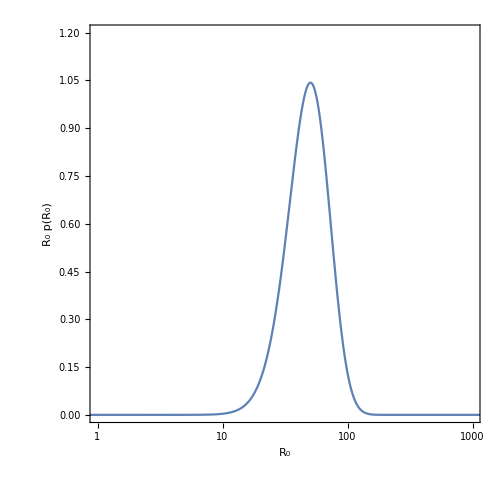

```mathematica
p2=LogLinearPlot[R*marginalPosterior1D["R",R],{R,min["R"],max["R"]},Evaluate@plotOptions,FrameLabel -> {"R_0", "R_0 p(R_0)"},PlotRange->{{1,10^3},{0,1.2}},FrameTicks->{{None,None},{True,None}}]
```

2D Marginalized posteriors

```mathematica
Clear[posteriorFit,marginalPosterior2D,marginalPosterior2DPlot];
posteriorFit[para1_?StringQ,para2_?StringQ]:=posteriorFit[para1,para2]=FindMaximum[marginalPosterior2D[para1,para2,x1,x2],{x1,median[para1],min[para1],max[para1]},{x2,median[para2],min[para2],max[para2]},PrecisionGoal->3]

constours[para1_?StringQ,para2_?StringQ]:=posteriorFit[para1,para2][[1]]*ⅇ^-dx2;
marginalPosterior2DPlot[para1_?StringQ,para2_?StringQ,opts:OptionsPattern[]]:=ContourPlot[marginalPosterior2D[para1,para2,x1,x2],{x1,min[para1]+0.05,max[para1]-0.1},{x2,min[para2]+0.05,max[para2]-0.1},Contours->constours[para1,para2],Evaluate[contourPlotOptions,plotOptions],opts]
```

## α-logM

{6.32554,{x1→2.58823,x2→0.899986}}

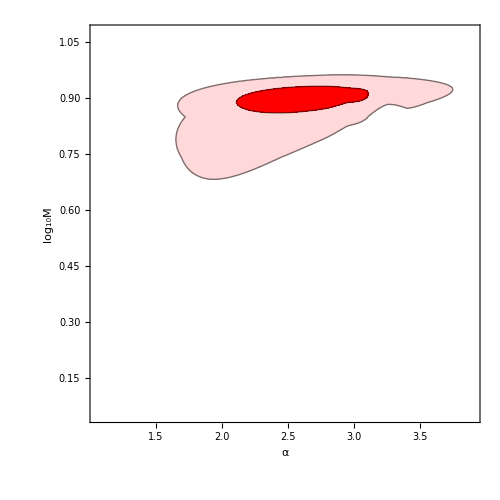

```mathematica
marginalPosterior2D["α","logM",α_?NumericQ,logM_?NumericQ]:=NIntegrate[post[logf,α,logM],{logf,min["logf"],max["logf"]},PrecisionGoal->3]

posteriorFit["α","logM"]

p1=plot2D["α","logM"]=marginalPosterior2DPlot["α","logM",PlotRange->{{1.5,4},{0.5,1}},PlotPoints->50,MaxRecursion->2,FrameLabel -> {"α","log_10M"},FrameTicks->{{True,None},{True,True}}]
```

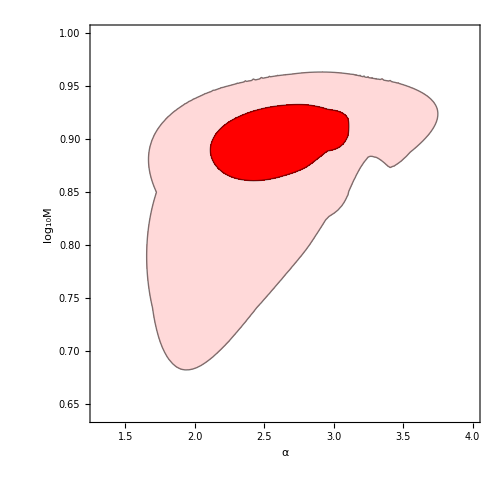

```mathematica
p3=Show[p1,PlotRange->{{1.3,4},{0.64,1}},FrameTicks->{{True,True},{True,True}}]
```

## Results

```mathematica
p1=-Graphics-;
p20=-Graphics-;
```

```mathematica
plotOptions0=Sequence[FrameStyle->(FontFamily->"Times"),BaseStyle->FontSize->25,LabelStyle->Black,Frame->True,Axes->False,PlotRangePadding->None,ImageSize->500,AspectRatio->1];
```

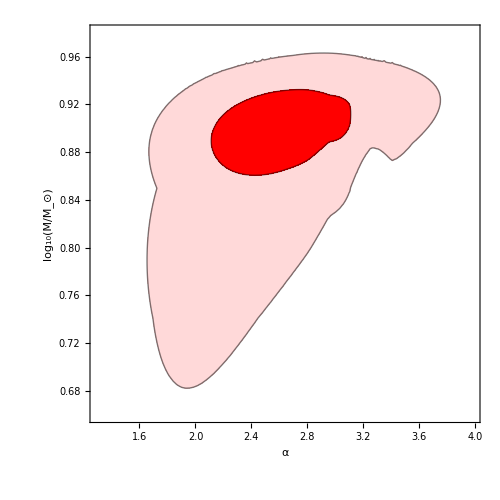

```mathematica
p3=Show[p1,PlotRange->{{1.3,3.98},{0.66,0.98}},FrameTicks->{{True,True},{True,True}},Evaluate@plotOptions0,FrameLabel -> {"α","log_10(M/M_⊙)"}]
```

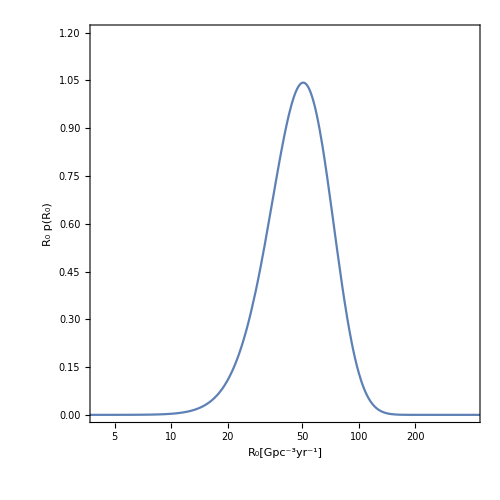

```mathematica
p2=Show[p20,Evaluate@plotOptions0,PlotRange->{{1.4,6},{0,1.2}},FrameLabel-> {"R_0[Gpc^-3yr^-1]", "R_0 p(R_0)"}]
```

```mathematica
range["logM"]
t1=10^range["logM"]
{t1[[2]],t1[[3]]-t1[[2]],t1[[1]]-t1[[2]]}
```

{0.614249,0.871411,0.945433,-0.257162,0.0740221}

{4.11386,7.43722,8.81928,0.553144,1.18583}

{7.43722,1.38205,-3.32337}

```mathematica
range["logf"]
t1=10^range["logf"]
{t1[[2]],t1[[3]]-t1[[2]],t1[[1]]-t1[[2]]}
```

{-2.78192,-2.54874,-2.33827,0.210461,-0.233184}

{0.00165227,0.0028266,0.00458908,1.62353,0.584542}

{0.0028266,0.00176248,-0.00117433}

```mathematica
range["α"]
```

{1.53342,2.40811,3.40679,0.998675,-0.874687}

```mathematica
range["R"]
```

{23.7335,48.1822,85.5508,37.3686,-24.4487}

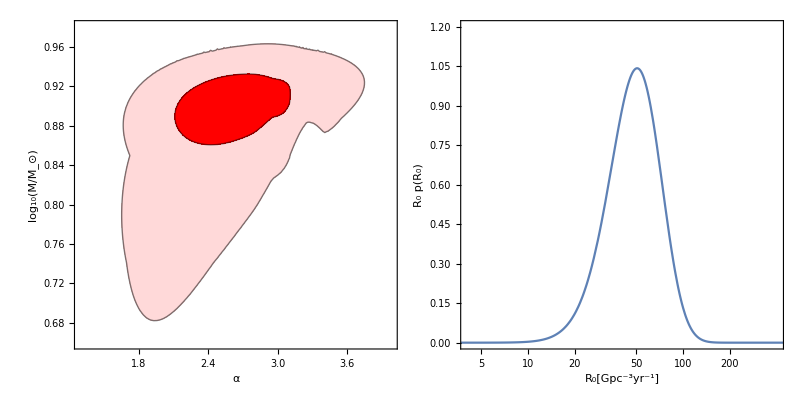

../latex/posterior-power.pdf

```mathematica
GraphicsGrid[{{p3,p2}},ImageSize->800,Spacings->Scaled[-.1]]
Export["../latex/posterior-power.pdf",%]
```